### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.006544,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1007→80.,j1008→80.,j1009→80.,j1010→80.,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80.,jt1017→80.,jt1018→0.,jt1019→80.,jt1020→0.,u1021→175.,u1022→95.,u1023→15.,u1024→175.,u1025→95.,u1026→15.,u1027→15.,u1028→175.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.62246×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.62246×10^-17

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→20.1639,u1022→17.582,u1023→15.,u1024→20.1639,u1025→17.582,u1026→15.,u1027→15.,u1028→20.1639|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.53876×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.53876×10^-17

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→21.3227,u1022→18.1613,u1023→15.,u1024→21.3227,u1025→18.1613,u1026→15.,u1027→15.,u1028→21.3227|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00518×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00518×10^-16

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→25.0478,u1022→20.0239,u1023→15.,u1024→25.0478,u1025→20.0239,u1026→15.,u1027→15.,u1028→25.0478|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→104.932,u1022→59.966,u1023→15.,u1024→104.932,u1025→59.966,u1026→15.,u1027→15.,u1028→104.932|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20583×10^-13

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→175.,u1022→95.,u1023→15.,u1024→175.,u1025→95.,u1026→15.,u1027→15.,u1028→175.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→742.811,u1022→378.906,u1023→15.,u1024→742.811,u1025→378.906,u1026→15.,u1027→15.,u1028→742.811|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→45695.9,u1022→22855.5,u1023→15.,u1024→45695.9,u1025→22855.5,u1026→15.,u1027→15.,u1028→45695.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→580101.,u1022→290058.,u1023→15.,u1024→580101.,u1025→290058.,u1026→15.,u1027→15.,u1028→580101.|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→581900.,u1022→290958.,u1023→15.,u1024→581900.,u1025→290958.,u1026→15.,u1027→15.,u1028→581900.|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→678389.,u1022→339202.,u1023→15.,u1024→678389.,u1025→339202.,u1026→15.,u1027→15.,u1028→678389.|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→796137.,u1022→398076.,u1023→15.,u1024→796137.,u1025→398076.,u1026→15.,u1027→15.,u1028→796137.|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→1.10875×10^6,u1022→554381.,u1023→15.,u1024→1.10875×10^6,u1025→554381.,u1026→15.,u1027→15.,u1028→1.10875×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→3.30779×10^6,u1022→1.6539×10^6,u1023→15.,u1024→3.30779×10^6,u1025→1.6539×10^6,u1026→15.,u1027→15.,u1028→3.30779×10^6|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→3.119×10^7,u1022→1.5595×10^7,u1023→15.,u1024→3.119×10^7,u1025→1.5595×10^7,u1026→15.,u1027→15.,u1028→3.119×10^7|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→4.81052×10^10,u1022→2.40526×10^10,u1023→15.,u1024→4.81052×10^10,u1025→2.40526×10^10,u1026→15.,u1027→15.,u1028→4.81052×10^10|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→1.12074×10^19,u1022→5.6037×10^18,u1023→15.,u1024→1.12074×10^19,u1025→5.6037×10^18,u1026→15.,u1027→15.,u1028→1.12074×10^19|>

```mathematica
alpha = 1.99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→3.98121×10^105,u1022→1.99061×10^105,u1023→15.,u1024→3.98121×10^105,u1025→1.99061×10^105,u1026→15.,u1027→15.,u1028→3.98121×10^105|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1007→80,j1008→80,j1009→80,j1010→80,j1011→0.,j1012→0.,j1013→0.,j1014→0.,jt1015→0.,jt1016→80,jt1017→80,jt1018→0.,jt1019→80,jt1020→0.,u1021→4.4098×10^106,u1022→2.2049×10^106,u1023→15.,u1024→4.4098×10^106,u1025→2.2049×10^106,u1026→15.,u1027→15.,u1028→4.4098×10^106|>

### What we this plot for?

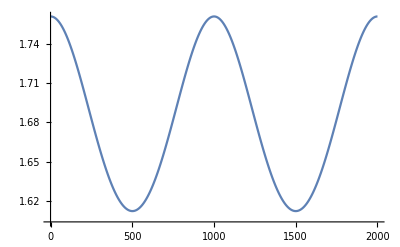

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.